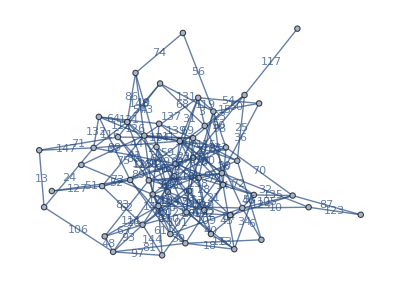

```mathematica
𝒢=GraphUnion@@ConnectedGraphComponents@RandomGraph[{54,148},EdgeWeight->RandomSample[Range[148]],EdgeLabels->"EdgeWeight"]
```

```mathematica
Select[VertexList[𝒢],OddQ[VertexDegree[𝒢,#]]&]
```

{1,2,5,6,7,9,10,11,13,16,17,19,24,28,30,31,32,34,35,36,38,39,41,44,46,48,49,51,53,54}

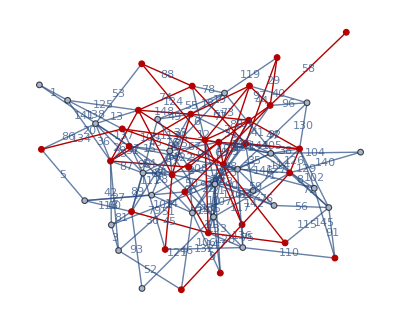

```mathematica
HighlightGraph[𝒢,{Subgraph[𝒢,Select[VertexList[𝒢],OddQ[VertexDegree[𝒢,#]]&]]}]
```

```mathematica
FindIndependentEdgeSet@Subgraph[𝒢,Select[VertexList[𝒢],OddQ[VertexDegree[𝒢,#]]&]]
```

{3<->11,7<->13,9<->46,12<->35,18<->49,19<->23,25<->53,39<->52,40<->54,43<->50}

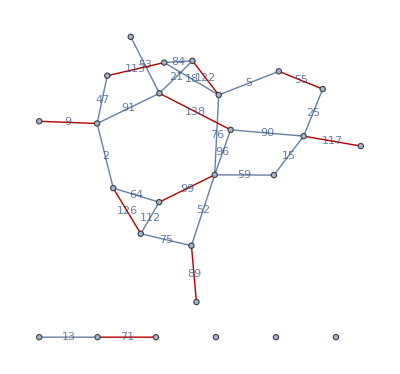

```mathematica
HighlightGraph[Graph[{3,4,7,8,9,11,12,13,15,18,19,23,25,35,37,39,40,41,42,43,46,49,50,52,53,54},{Null,SparseArray[Automatic,{26,26},0,{1,{{0,5,6,8,9,12,15,18,21,21,23,24,28,31,34,34,36,40,40,42,45,46,47,51,53,57,58},{{5},{6},{19},{20},{25},{23},{8},{17},{10},{1},{14},{21},{1},{7},{14},{6},{14},{17},{3},{13},{25},{4},{22},{12},{11},{16},{19},{20},{8},{23},{25},{5},{6},{7},{12},{24},{3},{7},{23},{26},{1},{12},{1},{12},{23},{5},{10},{2},{13},{17},{20},{16},{25},{1},{8},{13},{24},{17}}},Pattern}]},{EdgeLabels->{"EdgeWeight"},EdgeWeight->{52,99,59,96,76,53,113,47,13,75,89,64,112,126,2,84,18,71,117,25,15,90,21,122,55,91,9,138,5}}],%33]
```

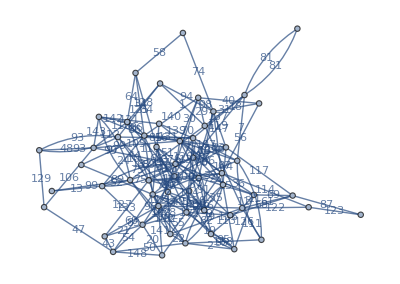

```mathematica
EdgeAdd[𝒢,FindIndependentEdgeSet@Subgraph[𝒢,Select[VertexList[𝒢],OddQ[VertexDegree[𝒢,#]]&]]]
```

```mathematica
EulerianGraphQ[EdgeAdd[𝒢,FindIndependentEdgeSet@Subgraph[𝒢,Select[VertexList[𝒢],EvenQ[VertexDegree[𝒢,#]]&]]]]
```

False

```mathematica
𝒢[{vertices_,edges_}]:=GraphUnion@@ConnectedGraphComponents@RandomGraph[{vertices,edges},EdgeWeight->RandomSample[Range[edges]],EdgeLabels->"EdgeWeight",VertexLabels->Automatic]
```

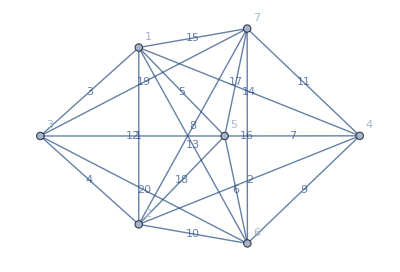

```mathematica
𝒢[{7,20}]
```

```mathematica
Select[VertexList[-Graphics-],OddQ[VertexDegree[-Graphics-,#]]&]
```

{3,4}

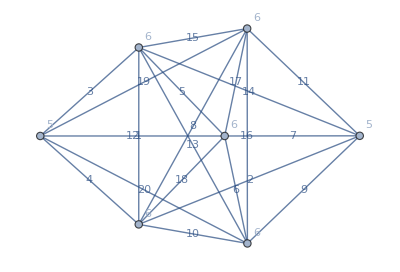

```mathematica
Graph[-Graphics-,VertexWeight->(VertexDegree[-Graphics-,#]&/@VertexList[-Graphics-]),VertexLabels->"VertexWeight"]
```

```mathematica
FindShortestTour[-Graphics-,Sequence@@Select[VertexList[-Graphics-], OddQ[VertexDegree[-Graphics-, #]] &]]
```

{40,{3,1,5,6,7,2,4}}

```mathematica
g=-Graphics-;
```

```mathematica
ℱ=FindMaximumFlow[g,{"Jesse","Mark","Erica","Toby","Jami","Chris"},{"Library","QA","Interface","Kernel","Sales"},"OptimumFlowData",VertexCapacity->ConstantArray[1,11]];
```

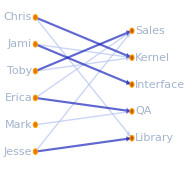

```mathematica
ℱ["FlowGraph"]
```

```mathematica
FindMaximumFlow[g,{"Jesse","Mark","Erica","Toby","Jami","Chris"},{"Library","QA","Interface","Kernel","Sales"},"OptimumFlowData",VertexCapacity->ConstantArray[1,11]];
```

```mathematica
MoleculeDraw[]
```

$Canceled

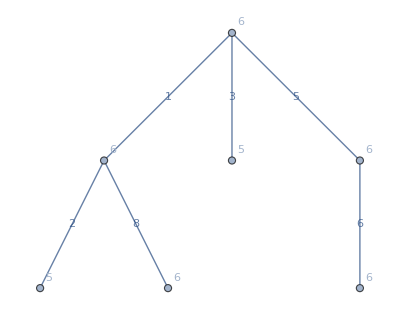

```mathematica
FindSpanningTree[-Graphics-]
```